```mathematica
Needs["MaTeX`"]; (* LaTeX Import *)
```

```mathematica
MaTeX["M_t = 4.07\\times10^{40}GeV \\frac{M_s R_s}{1- 2.964\\frac{M_s}{R_s}} \\left( \\frac{m_{\\chi} n_{\\chi}}{0.3GeV/cm^3} \\right) \\left (\\frac{v_0}{220 km/s} \\right)^{-1} \\left ( \\frac{t}{Gyr} \\right)f"](*Test for MaTeX*)
```

-Graphics-

Constants

```mathematica
Mpl = 1.22*10^(19); (* Planck Mass*)
Mcha =(2/Pi) *Mpl^2/mchi ; (*Chandrasekhar Mass*)
t =1; (* NS lifetime *)
Rs=12; (* NS Radius *)
v0 = 220; (* most probable speed of the velocity distribution *)
nc = 1; (* baryon density at the center NS center (fm^(-3)) *)
mn = 939.57; (* mass of nucleons (MeV) *)
G = 6.67*10^(-11); (*G constant*)
Mathematical Formalism
NBEC = 2.4*10^(35)*(1/0.3)^(3/2); (* Number of particles in BEC state*)
HR=- 1/(15360 * Pi *(G*Mcha)^2 ); (* Hawking Radiation *)
BA[lambdas_,cinfty_]:= (4 *Pi*lambdas* mn*nc*(G*Mcha)^2)/cinfty^3; (* Bondi Accretion *)
Mt[rhox_,mchi_,sigmax_,Ms_] := 4.07*10^(40)((Ms*Rs)/(1-(2.964*(Ms/Rs))))(rhox/0.3)(v0/220)^(-1)*t*(sigmax/10^(-45)); (* Mass of accumulated DM particles in NS as a function of DM density *)
Nuclear Models:
```

Mathematical Formalism

Nuclear Models:

```mathematica
MaTeX[" \\text{Lc92: }\\lambda_s =0.929, \\quad c_{\\infty} = 0.517 (c)"]
```

-Graphics-

```mathematica
MaTeX[" \\text{MSL1: }\\lambda_s = 1.415, \\quad c_{\\infty} = 0.634(c)"]
```

-Graphics-

```mathematica
MaTeX[" \\text{Adiabatic flow: }\\lambda_s =0.25, \\quad c_{\\infty} = 0.001"]
```

-Graphics-

```mathematica
(* List of rhox,Ms and values *)
```

```mathematica
rhoxlist=List[0.3,1,10^3];(* List of expected DM density values *)
```

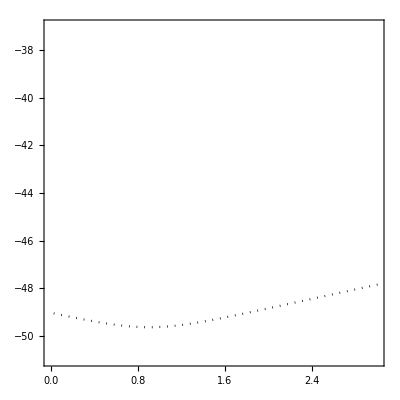

```mathematica
plt1=ContourPlot[{Mt[0.3,mchi,sigmax,1.4]+BA[1.415,0.634]+HR==0,Mt[0.3,mchi,sigmax,1.4]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-51),10^(-37)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->500,PerformanceGoal->"Quality",AspectRatio->1,PlotTheme->"Scientific",FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->Directive[Black,Dotted],PlotLegends->LineLegend[{Dotted,Black},{MaTeX["\\text{Zheng et al. (2015) for: } \\rho_{\\chi} = 0.3 GeV/cm^3 \\text{ with the MSL1 EoS}"]}]]
```

```mathematica
ContourPlot[sigmax==mchi*2*10^(-24),{mchi,10^(-2),10^3},{sigmax,10^(-80),10^(-20)},ScalingFunctions->{"Log","Log"},Contours->10^9,PlotPoints->100,FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},PlotLabel-> MaTeX["Bullet \\quad Cluster: \\sigma / m < 2 \\times 10^{-24}cm^2/GeV"]] ;(* Bullet Cluster's Exclusion *)
```

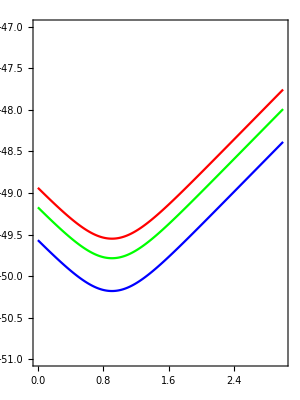

```mathematica
plt11=ContourPlot[{Mt[0.3,mchi,sigmax,1.2]+BA[0.929,0.517]+HR==0,Mt[0.3,mchi,sigmax,1.2]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-51),10^(-47)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->{Red},PlotLegends->{MaTeX["M_s = 1.2M_{\\odot} \\text{ for } \\rho_{\\chi} = 0.3 GeV/cm^3"]}];
plt22=ContourPlot[{Mt[0.3,mchi,sigmax,1.7]+BA[0.929,0.517]+HR==0,Mt[0.3,mchi,sigmax,1.7]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-51),10^(-47)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->{Green},PlotLegends->{MaTeX["M_s = 1.7 M_{\\odot} \\text{ for } \\rho_{\\chi} = 0.3 GeV/cm^3"]}];
plt33=ContourPlot[{Mt[0.3,mchi,sigmax,2.6]+BA[0.929,0.517]+HR==0,Mt[0.3,mchi,sigmax,2.6]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-51),10^(-47)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->{Blue},PlotLegends->{MaTeX["M_s = 2.6M_{\\odot} \\text{ for } \\rho_{\\chi} = 0.3 GeV/cm^3"]}];
Show[plt11,plt22,plt33]
```

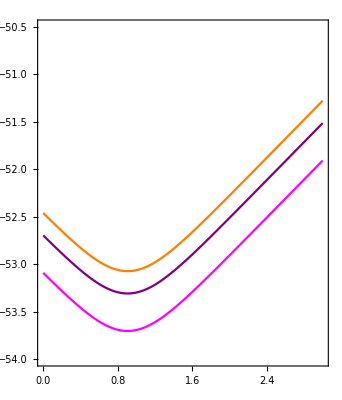

```mathematica
plt111=ContourPlot[{Mt[10^3,mchi,sigmax,1.2]+BA[0.929,0.517]+HR==0,Mt[10^3,mchi,sigmax,1.2]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-54),10^(-50.5)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->{Orange},PlotLegends->LineLegend[{Orange},{MaTeX["M_s = 1.2M_{\\odot} \\text{ for } \\rho_{\\chi} = 10^3 GeV/cm^3"]}]];
plt222=ContourPlot[{Mt[10^3,mchi,sigmax,1.7]+BA[0.929,0.517]+HR==0,Mt[10^3,mchi,sigmax,1.7]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-54),10^(-50.5)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->{Purple},PlotLegends->LineLegend[{Purple},{MaTeX["M_s = 1.7 M_{\\odot} \\text{ for } \\rho_{\\chi} = 10^3 GeV/cm^3"]}]];
plt333=ContourPlot[{Mt[10^3,mchi,sigmax,2.6]+BA[0.929,0.517]+HR==0,Mt[10^3,mchi,sigmax,2.6]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-54),10^(-50.5)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->{Magenta},PlotLegends->LineLegend[{Magenta},{MaTeX["M_s = 2.6M_{\\odot} \\text{ for } \\rho_{\\chi} = 10^3 GeV/cm^3"]}]];
Show[plt111,plt222,plt333]
```

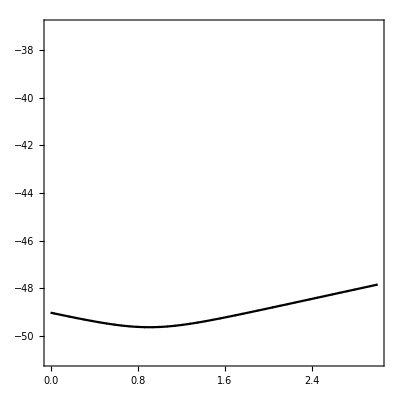

```mathematica
plt1=ContourPlot[{Mt[0.3,mchi,sigmax,1.4]+BA[1.415,0.634]+HR==0,Mt[0.3,mchi,sigmax,1.4]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-51),10^(-37)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->500,PerformanceGoal->"Quality",AspectRatio->1,PlotTheme->"Scientific",FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->Directive[Black,Dotted],PlotLegends->LineLegend[{Dotted,Black},{MaTeX["\\text{Zheng et al. (2015) for: } \\rho_{\\chi} = 0.3 GeV/cm^3 \\text{ with the MSL1 EoS}"]}]];
plt2=ContourPlot[{Mt[0.3,mchi,sigmax,1.4]+BA[0.929,0.517]+HR==0,-Mt[0.3,mchi,sigmax,1.4] + Mcha+ mchi*NBEC==0},{mchi,10^(0),10^3},{sigmax,10^(-51),10^(-47)},ScalingFunctions->{"Log10","Log10"},ColorFunction->GrayLevel,PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,PlotTheme->"Scientific",FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->Directive[Black,Thick],PlotLegends->LineLegend[{Black,Thick},{MaTeX["\\text{Zheng et al. (2015) for: } \\rho_{\\chi} = 0.3 GeV/cm^3 \\text{ with the Lc92 EoS}"]}]];
Show[plt1,plt2]
```

```mathematica
(* Find Min set of (mchi,sigmax) pair, e.g for plt2 *)
```

```mathematica
minplot= Bellplot1;
points=Cases[Normal@minplot,Line[pts_,___]:>pts,Infinity];
SetDirectory[NotebookDirectory[]];
data=Cases[minplot,GraphicsComplex[pts__]:>pts,Infinity];
Dimensions[data[[1]]];
data1 = data[[1,1;;All,All]]//MatrixForm;
(*Export["mfile.csv",data1] *)                                    (*Export data if needed*)
Min[points]                                                                           (* Min sigmax *)
test=Flatten@Position[points,Min[points]] ;  (* corresponding position of mchi for Min sigmax *)
exp=Extract[Part[data1,1,test,1] ,2];            (* point of plot for Min sigmax *)
minmass=10^(exp )                                                               (* Value of mchi for Min sigmax *)
```

Part::partw: Part 1 of {} does not exist.

∞

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Extract::partw: Part 2 of Part[] does not exist.

10^Extract[Part[],2]

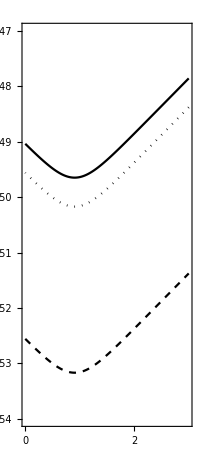

```mathematica
plt2=ContourPlot[{Mt[0.3,mchi,sigmax,1.4]+BA[0.929,0.517]+HR==0,-Mt[0.3,mchi,sigmax,1.4] + Mcha+ mchi*NBEC==0},{mchi,10^(0),10^3},{sigmax,10^(-54),10^(-47)},ScalingFunctions->{"Log10","Log10"},ColorFunction->GrayLevel,PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,PlotTheme->"Scientific",FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->Directive[Black,Thick],PlotLegends->LineLegend[{Black,Thick},{MaTeX["\\text{Zheng et al. (2015) for: } \\rho_{\\chi} = 0.3 GeV/cm^3 \\text{ with the Lc92 EoS}"]}]];
plotrhox1=ContourPlot[{Mt[1,mchi,sigmax,1.4]+BA[0.929,0.517]+HR==0,-Mt[1,mchi,sigmax,1.4]+ Mcha+ mchi*NBEC==0},{mchi,10^(0),10^3},{sigmax,10^(-54),10^(-48)},ScalingFunctions->{"Log10","Log10"},ColorFunction->GrayLevel,PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,PlotTheme->"Scientific",FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},PlotLegends->LineLegend[{Dotted,Black},{MaTeX["\\text{Zheng et al. (2015) for: } \\rho_{\\chi} = 1 GeV/cm^3 \\text{ with the Lc92 EoS}"]}],ContourStyle->Directive[Black,Dotted]];
plotrhox103=ContourPlot[{Mt[10^3,mchi,sigmax,1.4]+BA[0.929,0.517]+HR==0,-Mt[10^3,mchi,sigmax,1.4] + Mcha+ mchi*NBEC==0},{mchi,10^(0),10^3},{sigmax,10^(-54),10^(-48)},ScalingFunctions->{"Log10","Log10"},PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->Automatic,PlotTheme->"Scientific",FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},PlotLegends->LineLegend[{Dashed,Black},{MaTeX["\\text{Zheng et al. (2015) for: } \\rho_{\\chi} = 10^3 GeV/cm^3 \\text{ with the Lc92 EoS}"]}],ContourStyle->Directive[Black,Dashed]];
sumplot1=Show[plt2,plotrhox1,plotrhox103,PlotLegends->{MaTeX["\\rho_{\\chi} = 0.3 GeV/cm^3"],MaTeX["\\rho_{\\chi} = 1 GeV/cm^3"],MaTeX["\\rho_{\\chi} =10^3 GeV/cm^3"]}]
```

```mathematica
(* Bell et al. (2020) geometrical estimation of accretion*)
```

```mathematica
vstar=1100; (* Typical NS velocity (km/s)*)
```

```mathematica
Cgeom[R_,B_,rhox_,mchi_,sigmax_]:=3.85*10^(42)*(R/12)*(vstar/1100)^(-1)*(rhox/0.3)*t*sigmax/10^(-45);
```

```mathematica
BA2= (4 *Pi* lambdas* mn*nc*(G*Mcha)^2)/cinfty^3;
```

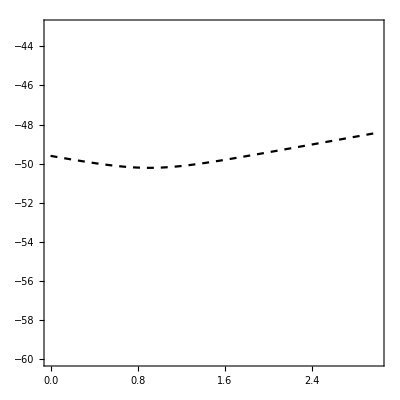

```mathematica
Bellplot1=ContourPlot[{Cgeom[12,0.7,0.3,mchi,sigmax]+BA[0.25,0.001]+HR==0,Cgeom[12,0.7,0.3,mchi,sigmax]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-60),10^(-43)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->1,PlotTheme->"Scientific",FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},PlotLegends->LineLegend[{Dashed,Black},{MaTeX["\\text{Bell et al. (2020) for: } \\rho_{\\chi} = 0.3 GeV/cm^3 \\text{ Adiabatic Flow}"]}],ContourStyle->Directive[Black,Dashed]]
```

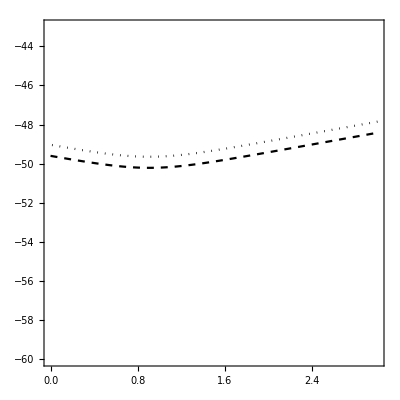

```mathematica
Show[Bellplot1,plt1]
```

```mathematica
(* Constraints by the thermalization time*)
```

```mathematica
MaTeX["t_{th} \\simeq 0.054yr \\left(\\frac{m_{\\chi}}{100GeV} \\right)^2 \\left(\\frac{2.1\\times 10^{-45}cm^2}{\\sigma _n} \\right) \\left( \\frac{10^5 K}{T} \\right)"]
```

-Graphics-

```mathematica
(*for the range of interest of the plots*)
```

```mathematica
plotthermal=ContourPlot[10^9==0.054*(mchi/100)^2 * (2.1*10^(-45)/sigmax),{mchi,10^(-3),10^(3)},{sigmax,10^(-60),10^(-40)},Exclusions->{10^9<0.054*(mchi/100)^2 * (2.1*10^(-45)/sigmax),{mchi,10^(-3),10^(3)},{sigmax,10^(-60),10^(-50)}},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->1,FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},PlotLegends->LineLegend[{MaTeX["\\text{No thermalization}"]}]];
```

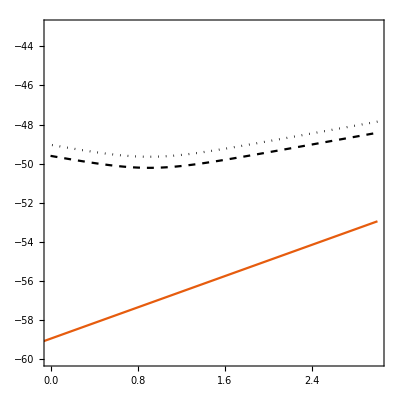

```mathematica
Show[Bellplot1,plt1,plotthermal]
```

```mathematica
(* Compare adiabatic flow to relativistic *)
```

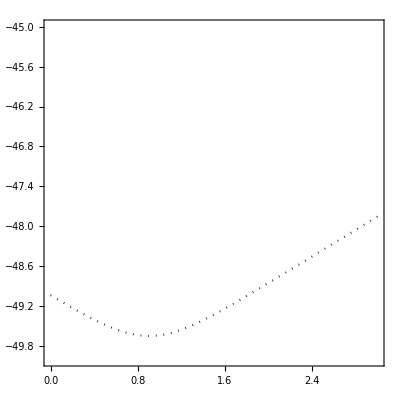

```mathematica
plt1dot=ContourPlot[{Mt[0.3,mchi,sigmax,1.4]+BA[0.25,0.001]+HR==0,Mt[0.3,mchi,sigmax,1.4]== Mcha+ mchi*NBEC},{mchi,10^(0),10^(3)},{sigmax,10^(-50),10^(-45)},ScalingFunctions->{"Log10","Log10"},PlotTheme-> "Scientific",PlotPoints->300,PerformanceGoal->"Quality",AspectRatio->1,PlotTheme->"Scientific",FrameLabel->{MaTeX["m_{\\chi} (GeV)"],MaTeX["\\sigma_{\\chi} (cm^2)"]},ContourStyle->Directive[Black,Dotted],PlotLegends->LineLegend[{Dotted,Black},{MaTeX["\\text{Zheng et al. (2015) for: } \\rho_{\\chi} = 0.3 GeV/cm^3 \\text{ with the MSL1 EoS}, Adiabatic flow"]}]]
```

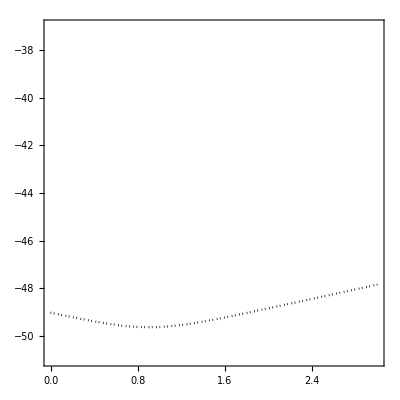

```mathematica
Show[plt1,plt1dot] (* no difference *)
```

```mathematica
a="C:\\Users\\nkout\\Desktop\\cdms\\CDMS_Si_c58_UpperLimit.dat";
data=Import[a,"Table"];
sigmaxdat=10^data[[;;,2]];
mchidat=10^data[[;;,1]];
pairUp[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
CDMSc58pair=pairUp[mchidat,sigmaxdat];
CDMSc58=ListLinePlot[CDMSc58pair,PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},PlotTheme->"Scientific",PlotLabels->Placed["CDMSc58",Above]];
```

```mathematica
a="C:\\Users\\nkout\\Desktop\\XENON\\XENON1T-s2only_data_release-5a364bc\\limits\\5a_results_si_nr.csv";
data=Import[a];
sigmaxdat=data[[2;;,2]];
mchidat=data[[2;;,1]];
pairUp[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
XENON1Tpair=pairUp[mchidat,sigmaxdat];
XENON1T=ListLinePlot[XENON1Tpair,PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},PlotTheme->"Scientific",PlotLabels->Placed["XENON1T-s2only",Above]];
```

```mathematica
a="C:\\Users\\nkout\\Desktop\\LUX\\LUX Run3+4 Combined Limit (90% CL).csv";
data=Import[a];
sigmaxdat=data[[2;;,3]];
mchidat=data[[2;;,1]];
pairUp[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
LUXpair=pairUp[mchidat,sigmaxdat];
LUXdat=ListLinePlot[LUXpair,PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},PlotTheme->"Scientific",PlotLabels->Placed["LUX Run3+4 Combined Limit (90% CL)",Above]];
```

```mathematica
a="C:\\Users\\nkout\\Desktop\\PandaX\\PandaX-II 2017.csv";
data=Import[a];
sigmaxdat=data[[2;;,2]];
mchidat=data[[2;;,1]];
pairUp[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
PandaXIIpair=pairUp[mchidat,sigmaxdat];
PandaXII=ListLinePlot[PandaXIIpair,PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},PlotTheme->"Scientific",PlotLabels->Placed["PandaX-II 2017",Above]];
```

```mathematica
a="C:\\Users\\nkout\\Desktop\\DAMA\\DAMA.csv";
data=Import[a];
sigmaxdat=data[[2;;,3]];
mchidat=data[[2;;,1]];
pairUp[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
DAMApair=pairUp[mchidat,sigmaxdat];
DAMA=ListLinePlot[DAMApair,PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},PlotTheme->"Scientific",PlotLabels->Placed["DAMA",Above]];
```

```mathematica
a="C:\\Users\\nkout\\Desktop\\CoGeNT\\CoGeNT.csv";
data=Import[a];
sigmaxdat=data[[2;;,2]];
mchidat=data[[2;;,1]];
pairUp[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
CoGeNTpair=pairUp[mchidat,sigmaxdat];
CoGeNT=ListLinePlot[CoGeNTpair,PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},PlotTheme->"Scientific",PlotLabels->Placed["CoGeNT",Above]];
```

```mathematica
a="C:\\Users\\nkout\\Desktop\\CDMS-II\\CDMS-II.csv";
data=Import[a];
sigmaxdat=data[[2;;,2]];
mchidat=data[[2;;,1]];
pairUp[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
CDMSIIpair=pairUp[mchidat,sigmaxdat];
CDMSII=ListLinePlot[CDMSIIpair,PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},PlotTheme->"Scientific",PlotLabels->Placed["CDMSII",Above]];
```

```mathematica
a="C:\\Users\\nkout\\Desktop\\DEAP-3600\\DEAP-3600.csv";
data=Import[a];
sigmaxdat=data[[2;;,2]];
mchidat=data[[2;;,1]];
pairUp[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
DEAP3600pair=pairUp[mchidat,sigmaxdat];
DEAP3600=ListLinePlot[DEAP3600pair,PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},PlotTheme->"Scientific",PlotLabels->Placed["DEAP3600",Above]];
```

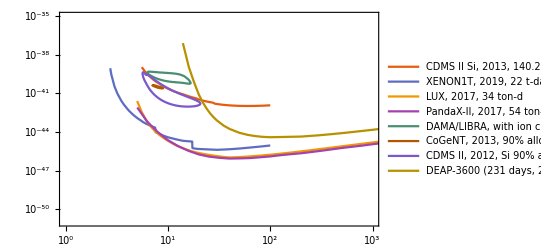

```mathematica
Expdata=ListLinePlot[{CDMSc58pair,XENON1Tpair,LUXpair,PandaXIIpair,DAMApair,CoGeNTpair,CDMSIIpair,DEAP3600pair},PlotRange->{{10^(0),10^(3)},{10^(-51),10^(-35)}},ScalingFunctions->{"Log10","Log10"},PlotRange->{{10^(0),10^(3)},{10^(-50),10^(-35)}},PlotTheme->"Scientific",PlotLegends->{"CDMS II Si, 2013, 140.2 kg-d","XENON1T, 2019, 22 t-day","LUX, 2017, 34 ton-d","PandaX-II, 2017, 54 ton-d","DAMA/LIBRA, with ion channeling, 3sigma","CoGeNT, 2013, 90% allowed region","CDMS II, 2012, Si 90% allowed region","DEAP-3600 (231 days, 2019)"}]
```

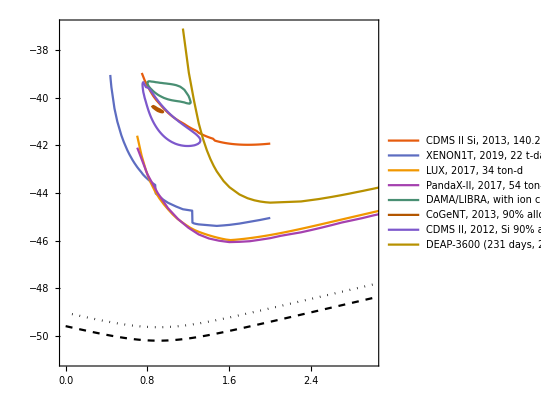

```mathematica
Show[plt1,Bellplot1,Expdata]
```